## An analytic Hopf-Cole solution to Burger's Equation w_t+w w_x=ν w_xx on a 2π-periodic domain

First, set the parameters for and examine an analytic solution to the heat equation u_t=νu_xx on a 2π-periodic domain.  This form was taken from Equation World (http://eqworld.ipmnet.ru/en/solutions/lpde/lpde101.pdf).

```mathematica
A=1; (* Magnitude *)
B=1; (* Phase Shift *)
Const=10000/9999; (* Constant offset *)
ν=1/100; (* Diffusion coefficient *)
μ=3; (* Frequency *)
u[x_,t_]:= A Exp[-ν μ^2 t]Cos[μ x + B]+Const
```

Ensure the closed-form function is a solution:

```mathematica
D[u[x,t],t]-ν D[u[x,t],{x,2}]//FullSimplify
```

0

Visually inspect the solution:

```mathematica
Plot3D[u[x,t],{x,0,2π},{t,0,1},PlotRange->Full]
```

-Graphics3D-

Employ the Hopf-Cole transformation to find w[x,t] in terms of u[x,t]:

```mathematica
w[x_,t_]=-2ν D[u[x,t],x]/u[x,t];
w[x,t]
```

(3 ⅇ^(-9 t/100) Sin[1+3 x])/(50 (10000/9999+ⅇ^(-9 t/100) Cos[1+3 x]))

Ensure the closed-form function is a solution:

```mathematica
D[w[x,t],t]+w[x,t] D[w[x,t],x] - ν D[w[x,t],{x,2}]//FullSimplify
```

0

Kick out the Burger' s problem initial condition for numerical use:

```mathematica
w[x,0]//FullSimplify
```

(3 Sin[1+3 x])/(50 (10000/9999+Cos[1+3 x]))

Visually inspect the solution:

```mathematica
Plot3D[w[x,t],{x,0,2π},{t,0,1},PlotRange->Full]
```

-Graphics3D-

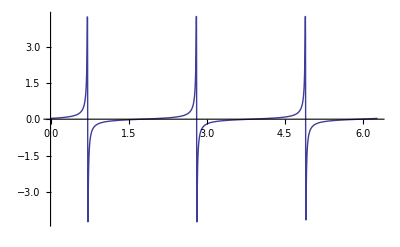

```mathematica
Plot[w[x,0],{x,0,2π},PlotRange->Full]
```

The heat equation parameters were chosen to produce a valid Hopf-Cole solution avoiding divide-by-zero problems.  Present are (hopefully) features sharp enough to exercise shock-capturing numerics and diffusive effects noticable but small enough to detect numerical dissipation.